# Dark SRF Sensitivity on Dark Photon

Zhen Liu (zliuphys@umn.edu)
These codes are accumulated through 2018- till now.
Current update (June. 2022): starting the analysis of the Dark Run1 data, which was taken around Apr. 2022. 
The new data taking also followed my earlier recommendation on having timed series of PSD, instead of only providing the averaged PSD. 
The new data taking also followed my earlier recommendation of narrowed scan range. 
We learned many many key features of the system, invalidated certain assumptions of our run0 analysis, and validated certain assumption of our run01 analysis. Another key difference is that the current run cannot get rid of “cross-talk”--this will worsen our results but provide me a lot more handles in tracking the cavity properties. 

Mar2025 Updates: ZL use it to re-calculate the sensitivity with better Michrophonics Modeling.

#### Plotting Standard

```mathematica
$CustomTicksPath = SetDirectory[NotebookDirectory[]<>"..\\..\\CodeReservaior\\CustomTicks"];
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"],Cell[StyleData["BoxData",All],FontFamily->"CMU Serif"],Cell[StyleData["TextData",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



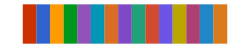

```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[112,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=112;
```

```mathematica
ColorData[colorselecitonumber][1]
```

RGBColor[0.790588, 0.201176, 0.]

## constants

```mathematica
ϵ0=8.854*10^-12 F m^-1;
μ0=4Pi*10^-7 Newton A^-2;
A=1 Coulomb/sec;
Tesla=1 Newton/A/m;
Newton=1 kg m/sec^2;
plank=4.14*10^-15 eV sec/(2Pi);(*hbar=1 actually*)
plankunbar=4.14*10^-15 eV sec;(*hbar=1 actually*)
plankconst=6.626*10^-34 J sec/(2Pi);(*hbar=1 actually*)
J=1 kg m^2/sec^2;
solunitless=3*10^8 ;
sol=3*10^8 m/sec;
F=Joule/V^2;
photonnumberperJoule1dot3GHz=1.602176565*10^-19 Joule/eV*1.3*10^9/sec*4.135667696×10^−15 eV sec/Joule(*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
photonnumberperJoule=1.602176565*10^-19 Joule/eV*1.3*10^9/sec*4.135667696×10^−15 eV sec/Joule(*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
photonnumberHzperJoule=1.602176565*10^-19 Joule/eV*1.3*10^9/sec*4.135667696×10^−15 eV sec/Joule (*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
```

8.61389×10^-25

8.61389×10^-25

8.61389×10^-25

-Graphics-

```mathematica
Tesla^2 m^3 plank/μ0/plankconst/(Kelvin *38.7 eV/300/Kelvin)
```

3.85433×10^25

```mathematica
(10^10/3*(10^-10 eV)^2/(2.3*10^9*2Pi /sec)^2 T)/plank^2*4Pi^2
```

14.5138 T

```mathematica
(10^10/3*(10^-10 eV)^2/(2.3*10^9*2Pi /sec)^2 Tesla)^2*(2.3*10^9*2Pi/sec)*(300*10^-6 m^3)*(365*24*3600 sec)/(4Kelvin)/(2μ0)*plank/plankconst/(10^10)
```

(2.16477×10^-34 eV^5 sec^4)/Kelvin

```mathematica
Tesla^2/μ0
```

(2500000 kg)/(m π sec^2)

```mathematica
frequencytable=Flatten[{Table[10^9 ω,{ω,0.1,3,0.1}],{5*10^7,5*10^6,5*10^5,5*10^4,5*10^3,10^7,10^6,10^5,10^4,10^3,5*10^9,8*10^9,10^10,2*10^10}},1]
Length[frequencytable]
```

{1.×10^8,2.×10^8,3.×10^8,4.×10^8,5.×10^8,6.×10^8,7.×10^8,8.×10^8,9.×10^8,1.×10^9,1.1×10^9,1.2×10^9,1.3×10^9,1.4×10^9,1.5×10^9,1.6×10^9,1.7×10^9,1.8×10^9,1.9×10^9,2.×10^9,2.1×10^9,2.2×10^9,2.3×10^9,2.4×10^9,2.5×10^9,2.6×10^9,2.7×10^9,2.8×10^9,2.9×10^9,3.×10^9,50000000,5000000,500000,50000,5000,10000000,1000000,100000,10000,1000,5000000000,8000000000,10000000000,20000000000}

44

```mathematica
$CustomTicksPath = SetDirectory[NotebookDirectory[]<>"..\\..\\scripts\\math_nb\\CustomTicks"];
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Zhen\Documents\GitHub\JitterModel\Research\..\..\scripts\math_nb\CustomTicks.

## Other limits

```mathematica
CROWSdata={{6.998971846764159*10^-10,0.9811597126105888},{
0.000010992485221306017,3.898663754783527*10^-9},{
0.000012495296770881312,1.5631226875419793*10^-8},{
0.00002910992562900514,1.2560189647413859*10^-7},{
0.00006279791222879355,0.0000019396310242980975},{
0.00009462968561687362,0.000007779710496636688},{
0.0000970862070012851,0.99713711656357}}
```

{{6.99897×10^-10,0.98116},{0.0000109925,3.89866×10^-9},{0.0000124953,1.56312×10^-8},{0.0000291099,1.25602×10^-7},{0.0000627979,1.93963×10^-6},{0.0000946297,7.77971×10^-6},{0.0000970862,0.997137}}

```mathematica
CMBdata={{1.726464029091634 10^-14,0.05324080954271558},{
1.726464029091634 10^-14,5.999104079881562 10^-7},{
1.9702464240535736 10^-13,2.352969097454555 10^-7},{
2.0213926625906278 10^-13,0.000006976926534148524},{
1.184759328703977 10^-12,0.000004284378783445524},{
5.954273331832952 10^-12,0.0000037987303976632477},{
2.6325505082194017 10^-11,0.000002530263918872383},{
1.3230472135586448 10^-10,8.082264862845412 10^-7},{
6.001411755821504 10^-10,1.9395110460829043 10^-7},{
1.0820481213379445 10^-9,8.576988204904801 10^-8},{
6.875887575517541 10^-8,8.98524686537015 10^-8},{
0.00002496090193044159,6.533407441472156 10^-8},{
0.00006120896958646347,1.4803959229175708 10^-7},{
0.00011035911756232787,5.044140186458462 10^-7},{
0.00013547192907857833,0.0000012390418522646481},{
0.00013547192907857833,0.9975904410313449}}
```

{{1.72646×10^-14,0.0532408},{1.72646×10^-14,5.9991×10^-7},{1.97025×10^-13,2.35297×10^-7},{2.02139×10^-13,6.97693×10^-6},{1.18476×10^-12,4.28438×10^-6},{5.95427×10^-12,3.79873×10^-6},{2.63255×10^-11,2.53026×10^-6},{1.32305×10^-10,8.08226×10^-7},{6.00141×10^-10,1.93951×10^-7},{1.08205×10^-9,8.57699×10^-8},{6.87589×10^-8,8.98525×10^-8},{0.0000249609,6.53341×10^-8},{0.000061209,1.4804×10^-7},{0.000110359,5.04414×10^-7},{0.000135472,1.23904×10^-6},{0.000135472,0.99759}}

```mathematica
Jupiterdata={{1.3953777087695384 10^-16,0.9607241807176014},{
1.9976237770206446 10^-16,0.638936885336235},{
3.0883465491642707 10^-16,0.39164454653425035},{
4.898560691179731 10^-16,0.2605025984587823},{
7.381603014008682 10^-16,0.1804832909120045},{
1.2012220279516255 10^-15,0.12505685308071104},{
2.005515520969056 10^-15,0.09026689611500045},{
3.4352543965402635 10^-15,0.06787346816357742},{
6.354511818767924 10^-15,0.053168261546839},{
1.0079167383426264 10^-14,0.049029234246443086},{
1.640201709764954 10^-14,0.05110683042735292},{
2.1743465673888532 10^-14,0.06019872768239584},{
2.8095071196259647 10^-14,0.08014685696048644},{
3.538354728900654 10^-14,0.10670149261540504},{
3.538354728900654 10^-14,0.16720881588120376
}}
```

{{1.39538×10^-16,0.960724},{1.99762×10^-16,0.638937},{3.08835×10^-16,0.391645},{4.89856×10^-16,0.260503},{7.3816×10^-16,0.180483},{1.20122×10^-15,0.125057},{2.00552×10^-15,0.0902669},{3.43525×10^-15,0.0678735},{6.35451×10^-15,0.0531683},{1.00792×10^-14,0.0490292},{1.6402×10^-14,0.0511068},{2.17435×10^-14,0.0601987},{2.80951×10^-14,0.0801469},{3.53835×10^-14,0.106701},{3.53835×10^-14,0.167209}}

```mathematica
Earthdata={{5.44880630564216 10^-15,0.9269039889619015},{
7.800515203965119 10^-15,0.6164445109216343},{
1.2372736200681117 10^-14,0.3936213365185442},{
2.4090694211869005 10^-14,0.19677627855261776},{
4.571963343703142 10^-14,0.1067388054843111},{
9.133062683048168 10^-14,0.06283085518552295},{
1.1502378943325788 10^-13,0.05560369179504262},{
2.0213926625906278 10^-13,0.05341981124466613},{
3.289449986453585 10^-13,0.055683456547976046},{
4.1428052748981246 10^-13,0.0580227328075224},{
6.404818826132212 10^-13,0.0712086881664536},{
8.490599507632327 10^-13,0.09101479988511844},{
1.1255631416906296 10^-12,0.16127747890603678},{
1.6113570399243163 10^-12,0.3651682345238209},{
2.248451694379249 10^-12,0.9735055019515539}}
```

{{5.44881×10^-15,0.926904},{7.80052×10^-15,0.616445},{1.23727×10^-14,0.393621},{2.40907×10^-14,0.196776},{4.57196×10^-14,0.106739},{9.13306×10^-14,0.0628309},{1.15024×10^-13,0.0556037},{2.02139×10^-13,0.0534198},{3.28945×10^-13,0.0556835},{4.14281×10^-13,0.0580227},{6.40482×10^-13,0.0712087},{8.4906×10^-13,0.0910148},{1.12556×10^-12,0.161277},{1.61136×10^-12,0.365168},{2.24845×10^-12,0.973506}}

```mathematica
Coulombdata={{1.44293436043621 10^-14,1.0071227940257619},{
2.0738666222109787 10^-13,0.055648423795317245},{
6.506630796081977 10^-9,0.000001499239842528702},{
6.701910597862602 10^-8,1.5915105016632886 10^-7},{
3.4556312857541637 10^-7,4.1449116493534844 10^-8},{
5.62341325190349 10^-7,3.11642328760205 10^-8},{
8.919540170609397 10^-7,2.5424539074084277 10^-8},{
0.000001414767033672739,2.4422553662458237 10^-8},{
0.0000016927619579606218,2.5446771924133512 10^-8},{
0.0000030520317068844263,3.389450355790406 10^-8},{
0.00003482988614452045,1.8899740006514449 10^-7},{
0.000047371124986312394,2.730587201910568 10^-7},{
0.00008324855661407094,6.990412338505766 10^-7},{
0.00013547192907857833,0.0000022862093145392613},{
0.0002571003925419703,0.000014374264757413162},{
0.0004879284756246082,0.00012028255079189256},{
0.0007166518382193539,0.0005680323842710022},{
0.0011079509850538286,0.004379231887471609},{
0.0012594218765929741,0.007149865549308395
}}
```

{{1.44293×10^-14,1.00712},{2.07387×10^-13,0.0556484},{6.50663×10^-9,1.49924×10^-6},{6.70191×10^-8,1.59151×10^-7},{3.45563×10^-7,4.14491×10^-8},{5.62341×10^-7,3.11642×10^-8},{8.91954×10^-7,2.54245×10^-8},{1.41477×10^-6,2.44226×10^-8},{1.69276×10^-6,2.54468×10^-8},{3.05203×10^-6,3.38945×10^-8},{0.0000348299,1.88997×10^-7},{0.0000473711,2.73059×10^-7},{0.0000832486,6.99041×10^-7},{0.000135472,2.28621×10^-6},{0.0002571,0.0000143743},{0.000487928,0.000120283},{0.000716652,0.000568032},{0.00110795,0.00437923},{0.00125942,0.00714987}}

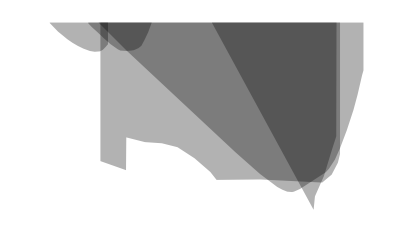

```mathematica
otherlimits=ListLogLogPlot[{{#[[1]],#[[2]]}&/@CROWSdata,{#[[1]],#[[2]]}&/@CMBdata,{#[[1]],#[[2]]}&/@Jupiterdata,{#[[1]],#[[2]]}&/@Earthdata,{#[[1]],#[[2]]}&/@Coulombdata},Joined->True,Filling->Top,FillingStyle->{Gray,Lighter[Gray],Opacity[0.3]},PlotStyle->None,Axes->False]
```

```mathematica
Sqrt[1-0.995^2]
```

0.0998749

## Loading data so we can skip various steps

```mathematica
{resultsG,resultsGwR,resultsGwZR,resultsGwithDerivatives,resultsGwRwithDerivatives,resultsGwRZwithDerivatives,resultsGwRZfullwithDerivatives}=Import[NotebookDirectory[]<>"..\\..\\DarkSRF\\CavitingBSM\\research\\Gcalculationresults.m"];
```

```mathematica
run1data=Import[NotebookDirectory[]<>"..\\..\\DarkSRF\\CavitingBSM\\research\\Run1Data.xlsx"][[1]];
```

```mathematica
run1data13=Import[NotebookDirectory[]<>"..\\..\\DarkSRF\\CavitingBSM\\research\\Run1Data13.csv"];
```

```mathematica
run1data14=Import[NotebookDirectory[]<>"..\\..\\DarkSRF\\CavitingBSM\\research\\Run1Data14.xlsx"][[1]];
```

# Theory Calculation

## Calculation (current-version)

## New discussion May.08. 2020

Pd = (Eacc*L)^2/(R/Q*Q0)

Q0 = omega*U/Pd

R/Q = 105 Ohms for this cavity

Epeak = 1.88 Eacc;

Use Q-loaded

# Data Treatment (run0)

## (Run0) Data Set 12

### Plot

```mathematica
peakcoordinate=SortBy[run1data,Last][[-1]]
```

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[run1data,Last].

Last

```mathematica
N[peakcoordinate[[1]],10]
```

Part::partd: Part specification Last⟦1⟧ is longer than depth of object.

Last⟦1⟧

```mathematica
1.29804120494749*^9
```

1.29804×10^9

ColorData::notent: colorselecitonumber is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

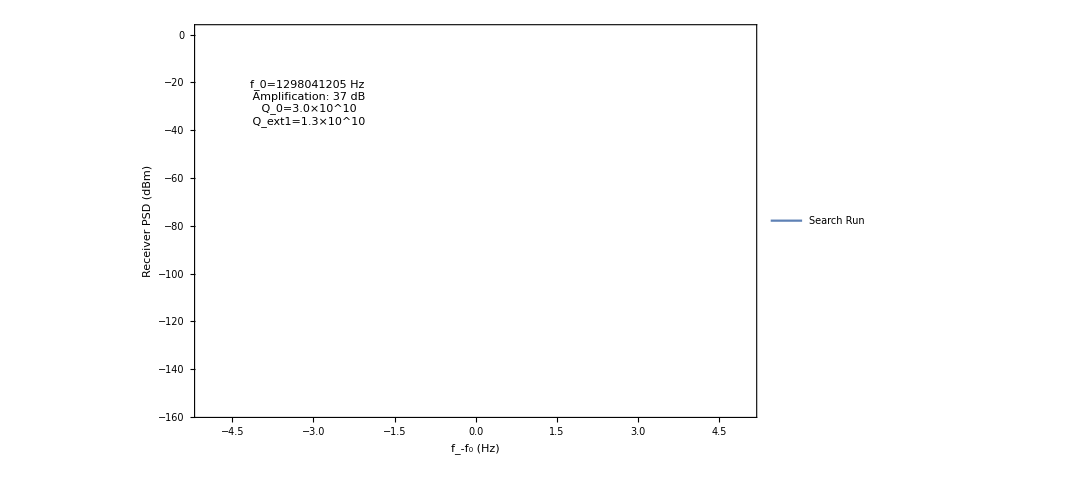

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*)},Joined->True,PlotRange->{{-5,5},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->20,ImageSize->800,FrameLabel->{{"Receiver PSD (dBm)",""},{"f_-f_0 (Hz)",""}},PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,ColorData[colorselecitonumber][1]},{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->Bottom,
Epilog->{Inset["f_0=1298041205 Hz\n Amplification: 37 dB\n Q_0=3.0×10^10\n Q_ext1=1.3×10^10",Scaled[{0.2,0.8}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]]
```

```mathematica
subpanel=ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*)},Joined->True,PlotRange->{{-1000,1000},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->10,ImageSize->300,FrameLabel->{{Style["Receiver PSD (dBm)",FontFamily->"CMU Serif"],""},{Style["f_-f_0 (Hz)",FontFamily->"CMU Serif"],""}},Axes->False,PlotStyle->{{Thin,ColorData[colorselecitonumber][2]},{Dashed,Thin,ColorData[colorselecitonumber][1]},{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}}]
```

ColorData::notent: colorselecitonumber is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

-Graphics-

ColorData::notent: colorselecitonumber is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

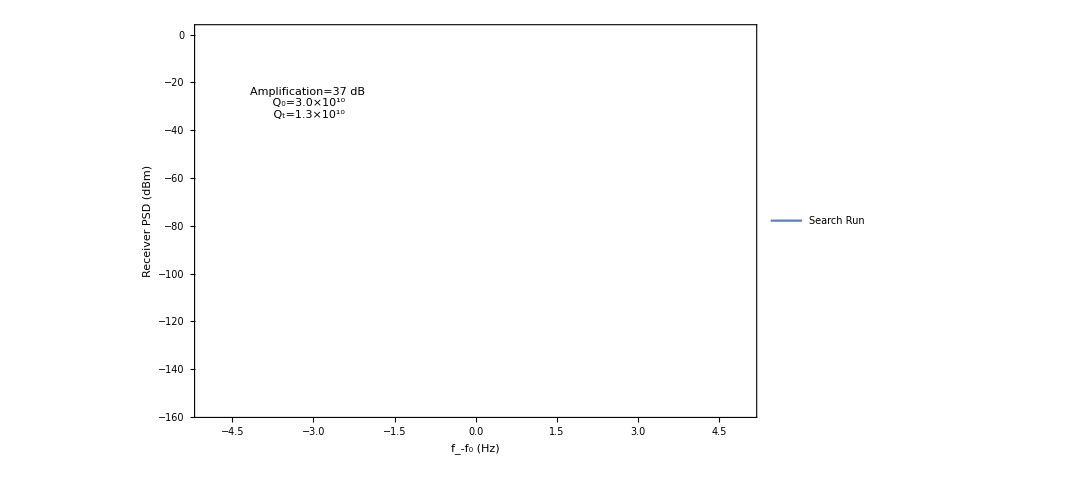

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*)},Joined->True,PlotRange->{{-5,5},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->24,ImageSize->800,FrameLabel->{{Style["Receiver PSD (dBm)",FontFamily->"CMU Serif"],""},{Style["f_-f_0 (Hz)",FontFamily->"CMU Serif"],""}},PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,ColorData[colorselecitonumber][1]},{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->Bottom,
(*Epilog->{Inset["f_0=1298041205 Hz\n Amplification=37 dB\n Q_0=3.0×10^10\n Q_ext1=1.3×10^10",Scaled[{0.2,0.8}]],Inset[subpanel,Scaled[{0.78,0.78}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]*)
Epilog->{Inset[Style[(*Subscript[f, 0]=1298041205 Hz\n *)"Amplification=37 dB\n Q_0=3.0×10^10\n Q_t=1.3×10^10",FontFamily->"CMU Serif"],Scaled[{0.2,0.8}]],Inset[subpanel,Scaled[{0.78,0.78}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]]
```

```mathematica
Export[NotebookDirectory[]<>"PSD_receiver_01242023_ZL.pdf",%]
```

C:\Users\Zhen\Documents\GitHub\JitterModel\Research\PSD_receiver_01242023_ZL.pdf

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First],{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First](*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*)},Joined->True,PlotRange->{{-5,5},{-155.5,Full}}]
```

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[run1data,Last].

Part::take: Cannot take positions -10 through -1 in SortBy[run1data,Last].

Part::pkspec1: The expression SortBy[run1data,Last] cannot be used as a part specification.

Part::partd: Part specification Last⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression {run1data-Last⟦1⟧,Last} cannot be used as a part specification.

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[run1data14,Last].

Part::take: Cannot take positions -10 through -1 in SortBy[run1data14,Last].

Part::pkspec1: The expression SortBy[run1data14,Last] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification Last⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

### Plot with Errorband (11/17/2022)

```mathematica
peakcoordinate=SortBy[run1data,Last][[-1]]
```

{1.29804×10^9,-151.809}

```mathematica
N[peakcoordinate[[1]],10]
```

1.29804×10^9

```mathematica
1.29804120494749*^9
```

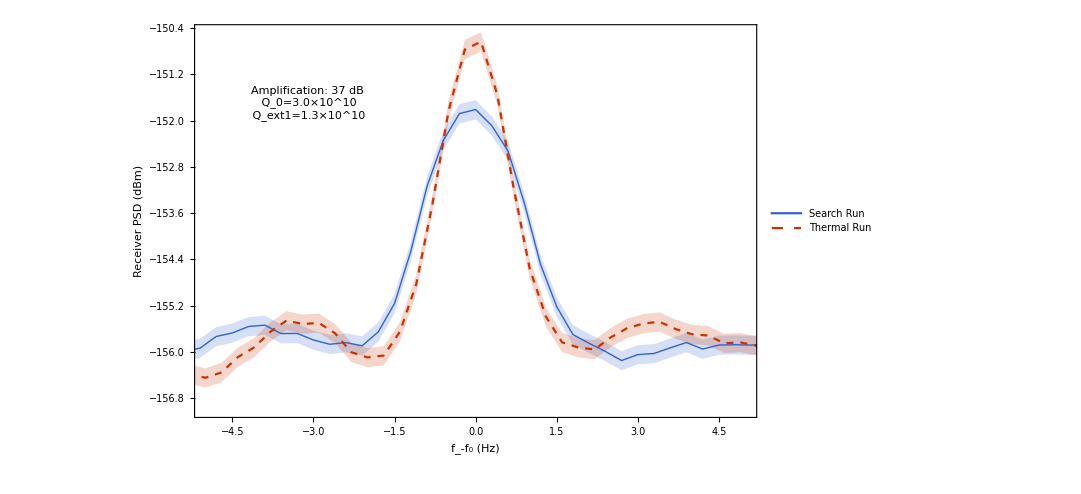

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*),{#[[1]]-peakcoordinate[[1]],Log10[10^(#[[2]]/10)*(1-1/Sqrt[independentmeasurements])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]],Log10[10^(#[[2]]/10)*(1+1/Sqrt[independentmeasurements])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,Log10[10^(#[[2]]/10)*(1-1/Sqrt[independentmeasurements])]*10}&/@run1data14,{#[[1]]-peakcoordinate[[1]]-3.5,Log10[10^(#[[2]]/10)*(1+1/Sqrt[independentmeasurements])]*10}&/@run1data14},Joined->True,PlotRange->{{-5,5},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->20,ImageSize->800,FrameLabel->{{"Receiver PSD (dBm)",""},{"f_-f_0 (Hz)",""}},PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,ColorData[colorselecitonumber][1]},None,None,None,None,{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->{3->{{4},Directive[Opacity[0.2],ColorData[colorselecitonumber][2]]},5->{{6},Directive[Opacity[0.2],ColorData[colorselecitonumber][1]]}},
Epilog->{Inset[(*Subscript[f, 0]=1298041205 Hz\n *)"Amplification: 37 dB\n Q_0=3.0×10^10\n Q_ext1=1.3×10^10",Scaled[{0.2,0.8}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]]
```

```mathematica
aveargesideband14=Mean[#[[2]]&/@SortBy[SortBy[run1data14,Last][[1;;-11]],First]]
aveargesideband=Mean[#[[2]]&/@SortBy[SortBy[run1data,Last][[1;;-11]],First]]
```

-155.817

-155.805

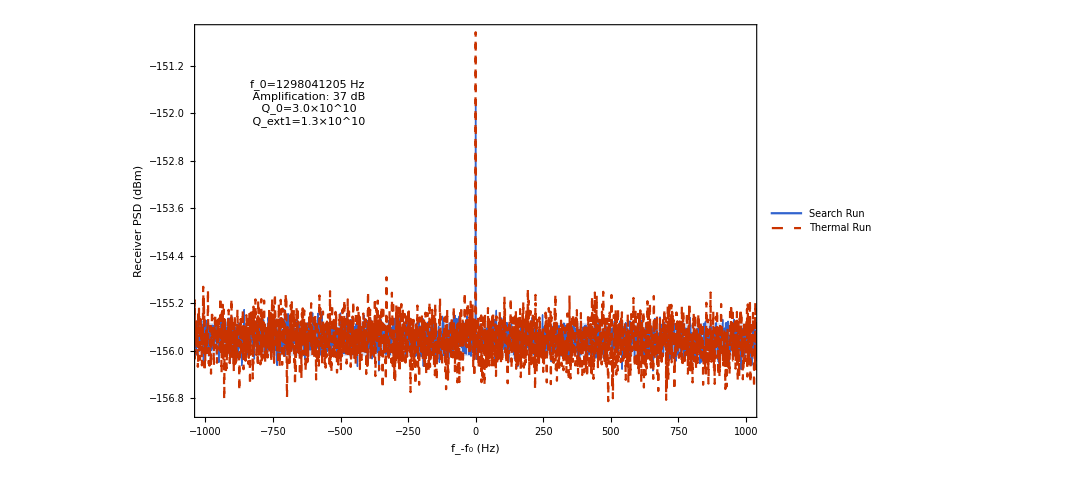

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*),
{#[[1]]-peakcoordinate[[1]],Log10[10^(aveargesideband/10)*(1-1/Sqrt[independentmeasurements11182022])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]],Log10[10^(aveargesideband/10)*(1+1/Sqrt[independentmeasurements11182022])]*10}&/@run1data},Joined->True,PlotRange->{{-1000,1000},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->20,ImageSize->800,FrameLabel->{{"Receiver PSD (dBm)",""},{"f_-f_0 (Hz)",""}},Filling->{3->{{4},Directive[Opacity[0.2],ColorData[colorselecitonumber][2]]}},PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,ColorData[colorselecitonumber][1]},None,None,None,None,{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->{3->{4},5->{6}},
Epilog->{Inset["f_0=1298041205 Hz\n Amplification: 37 dB\n Q_0=3.0×10^10\n Q_ext1=1.3×10^10",Scaled[{0.2,0.8}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]]
```

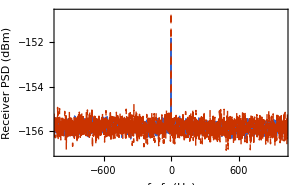

```mathematica
subpanel=ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*),{#[[1]]-peakcoordinate[[1]],Log10[10^(aveargesideband/10)*(1-1/Sqrt[independentmeasurements11182022])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]],Log10[10^(aveargesideband/10)*(1+1/Sqrt[independentmeasurements11182022])]*10}&/@run1data},Joined->True,PlotRange->{{-1000,1000},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->10,ImageSize->300,FrameLabel->{{"Receiver PSD (dBm)",""},{"f_-f_0 (Hz)",""}},Axes->False,Filling->{3->{{4},Directive[Opacity[0.9],ColorData[colorselecitonumber][2]]}},PlotStyle->{{Thin,ColorData[colorselecitonumber][2]},{Dashed,Thin,ColorData[colorselecitonumber][1]},None,None,Cyan,Cyan,{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}}]
```

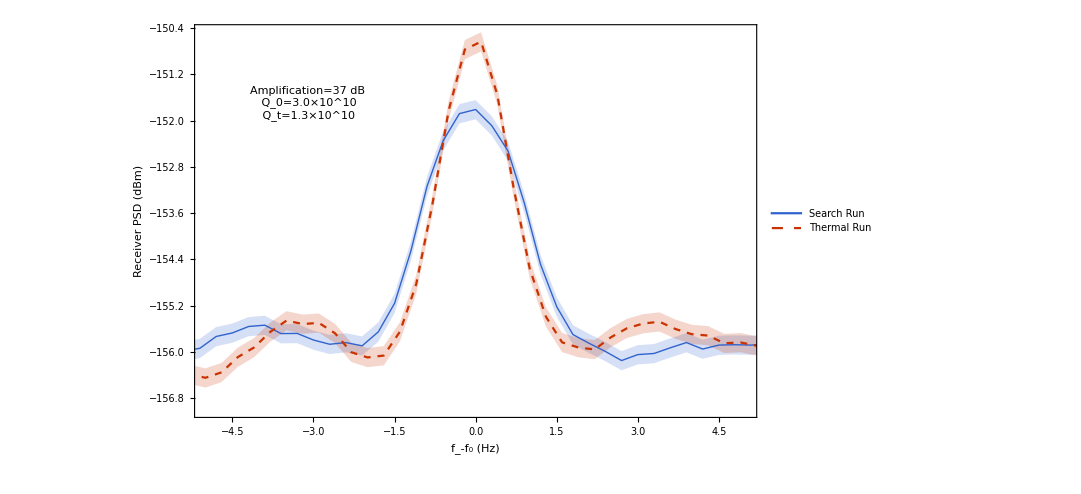

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,#[[2]]}&/@run1data14(*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*),{#[[1]]-peakcoordinate[[1]],Log10[10^(#[[2]]/10)*(1-1/Sqrt[independentmeasurements])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]],Log10[10^(#[[2]]/10)*(1+1/Sqrt[independentmeasurements])]*10}&/@run1data,{#[[1]]-peakcoordinate[[1]]-3.5,Log10[10^(#[[2]]/10)*(1-1/Sqrt[independentmeasurements])]*10}&/@run1data14,{#[[1]]-peakcoordinate[[1]]-3.5,Log10[10^(#[[2]]/10)*(1+1/Sqrt[independentmeasurements])]*10}&/@run1data14},Joined->True,PlotRange->{{-5,5},{-157,Full}},Frame->True,FrameStyle->Black,BaseStyle->20,ImageSize->800,FrameLabel->{{"Receiver PSD (dBm)",""},{"f_-f_0 (Hz)",""}},PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,ColorData[colorselecitonumber][1]},None,None,None,None,{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->{3->{{4},Directive[Opacity[0.2],ColorData[colorselecitonumber][2]]},5->{{6},Directive[Opacity[0.2],ColorData[colorselecitonumber][1]]}},
Epilog->{Inset[(*Subscript[f, 0]=1298041205 Hz\n *)"Amplification=37 dB\n Q_0=3.0×10^10\n Q_t=1.3×10^10",Scaled[{0.2,0.8}]],Inset[subpanel,Scaled[{0.78,0.78}]]},PlotLegends->Placed[Style[#,20,FontFamily->"CMU Serif"]&/@{"Search Run","Thermal Run"},{0.2,0.5}]]
```

```mathematica
Export[NotebookDirectory[]<>"PSD_receiver_01112023_ZL.pdf",%]
```

C:\Users\novar\OneDrive\pre2017\文档\GitHub\DarkSRF\CavitingBSM\research\PSD_receiver_01112023_ZL.pdf

```mathematica
ListPlot[{{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First],{#[[1]]-peakcoordinate[[1]],#[[2]]}&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First](*,{#[[1]]-referencefrequency,#[[2]]}&/@SortBy[SortBy[run1data13,Last][[-7;;-1]],First]*)},Joined->True,PlotRange->{{-5,5},{-155.5,Full}}]
```

### 2022 Paper input parameters (Updated Nov.15.2022, thinking more carefully about factor of 2Pis)

-Graphics-

```mathematica
peakcoordinate=SortBy[run1data,Last][[-1]];
Qload=8.9*10^9;
Qemitterload=1.6*10^9;
amplificationfactor=1/10^(37/10);
NumberForm[peakcoordinate[[1]],200]
peakfrequency=peakcoordinate[[1]];
peakangularfrequency=2Pi peakfrequency;
independentmeasurements=Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]
photonnumberperJoulePeakfrequency=1.602176565*10^-19 Joule/eV*peakfrequency/sec*4.135667696×10^−15 eV sec/Joule(*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
signalregionbackground=%/photonnumberperJoulePeakfrequency/Joule
signalregionbackground/Sqrt[independentmeasurements]
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-4;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
%/photonnumberperJoulePeakfrequency/Joule
%/Sqrt[independentmeasurements]
```

1.29804120494749×10^9

686.043

8.60091×10^-25

2.06977×10^-21 Joule

2406.45

91.8757

1.02951×10^-21 Joule

1196.98

45.6994

```mathematica
signalregionbackground
```

2406.45

Emitter cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
0.6*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

0.486765

26.8732

```mathematica
(*Note added 11/08/2022; I believe this is the integrated power in the cavity using the measured E fields and H fields*)
power=1706.8665784314976;
Eacc=-709.5009351205365;
lowPphotoncount=1/2ϵ0 power*V^2/m^2*m^3*(6.2*10^6 /Eacc)^2/photonnumberperJoulePeakfrequency/Joule
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/(4.5*10^10)
Log10[%*10^3]*10(*to dBm*)
```

6.70876×10^23

0.577014

2.94127

34.6853

0.577014

0.104578

20.1944

Receiver cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
4.8*10^-21*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

3.89412×10^-21

-174.096

```mathematica
peakangularfrequency
peakfrequency
```

8.15583×10^9

1.29804×10^9

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*Hz/Watt*Joule//Total
%*peakangularfrequency/Qload/Joule
Log10[%*10^3]*10(*to dBm*)
```

3.29413×10^-22 Joule

3.0187×10^-22

-185.202

```mathematica
Log10[Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*10^3]*10//N
```

-187.87

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-1;;-1]],First]*Qextreceiver/Q0receiver*10^3]*10//N
Log10[Mean[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First]]*Qextreceiver/Q0receiver*10^3]*10//N
```

-188.834

-151.834

0.162722

-0.169057

{-192.441}

-196.434

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
independentmeasurements14=Min[1.83*345sec/(Qload/(peakfrequency) sec)*Sqrt[1.83*345/(345/(Qload/peakfrequency))]//N,345]
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%%
```

-188.589

-151.589

326.171

0.234049

-0.247384

```mathematica
Q0Watt2PhotonNumber=(Q0receiver/peakangularfrequency)*2Pi*Joule/photonnumberperJoulePeakfrequency/Joule(*Here I am integrating over the window in frequency, not in angular frequency, so 2Pi is needed*)
```

2.68713×10^25

```mathematica
Qextreceiver/Q0receiver
```

0.433333

```mathematica
Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]Watt*(Qload)/(peakangularfrequency Hz)*Qextreceiver/Q0receiver(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule/photonnumberperJoulePeakfrequency/Joule//Total
```

1042.79

2406.45

```mathematica
Qload
Qextreceiver
```

8.9×10^9

1.3×10^10

```mathematica
searchmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
searchmeanrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements] Q0Watt2PhotonNumber
thermalmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
thermalrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements14] Q0Watt2PhotonNumber
```

3515.04

134.201

3718.79

205.911

```mathematica
Log10[Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)]*10+30
```

-188.834

```mathematica
bkg95CLnumber=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurements]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 3515.04+x at position 2 should be a machine-size real number.

248.371

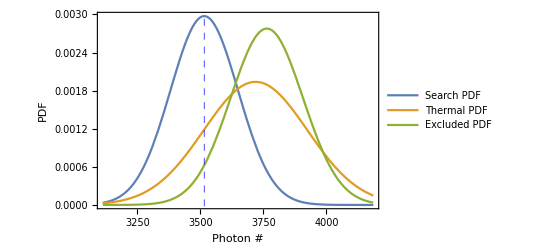

```mathematica
Plot[{PDF[NormalDistribution[searchmean,searchmeanrms],x],PDF[NormalDistribution[thermalmean,thermalrms],x],PDF[NormalDistribution[searchmean+bkg95CLnumber,(searchmean+bkg95CLnumber)/Sqrt[independentmeasurements]],x]},{x,searchmean-3searchmeanrms,searchmean+5searchmeanrms},GridLines->{{searchmean}},GridLinesStyle->Directive[Blue,Thick,Dashed],Frame->True,PlotLegends->{"Search PDF","Thermal PDF","Excluded PDF"},FrameLabel->{"Photon #","PDF"}]
```

```mathematica
Log10[(searchmean+bkg95CLnumber)/Q0Watt2PhotonNumber]*10+30
Log10[(searchmean)/Q0Watt2PhotonNumber]*10+30
%%-%
```

-188.537

-188.834

0.296515

```mathematica
sidebanddata=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First];
bkgnumber=Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms=StandardDeviation[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber/bkgrms
Sqrt[independentmeasurements]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec)*Sqrt[1328/(2430/(Qload/peakangularfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakangularfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakangularfrequency))]//N,1328]]//N
```

125.436

4.3506

28.8319

26.1924

18.8258

36.4417

15.5767

36.4417

26.1924

36.4417

28.9058

36.4417

```mathematica
sidebanddata14=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[1;;-11]],First];
bkgnumber14=Mean[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms14=StandardDeviation[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber14/bkgrms14
```

125.312

8.35933

14.9907

```mathematica
independentmeasurements11182022=Min[2430sec/(13*10^9/(peakfrequency) sec),1328]
```

242.634

### 2022 Paper input parameters (Updated May.04.2023)

-Graphics-

```mathematica
peakcoordinate=SortBy[run1data,Last][[-1]];
Qload=8.9*10^9;
Qemitterload=1.6*10^9;
amplificationfactor=1/10^(35.2/10);
NumberForm[peakcoordinate[[1]],200]
peakfrequency=peakcoordinate[[1]];
peakangularfrequency=2Pi peakfrequency;
independentmeasurements=Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]
photonnumberperJoulePeakfrequency=1.602176565*10^-19 Joule/eV*peakfrequency/sec*4.135667696×10^−15 eV sec/Joule(*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
signalregionbackground=%/photonnumberperJoulePeakfrequency/Joule
signalregionbackground/Sqrt[independentmeasurements]
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-4;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
%/photonnumberperJoulePeakfrequency/Joule
%/Sqrt[independentmeasurements]
```

1.29804120494749×10^9

686.043

8.60091×10^-25

3.13272×10^-21 Joule

3642.31

139.06

1.55823×10^-21 Joule

1811.7

69.1688

```mathematica
signalregionbackground
```

3642.31

Emitter cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
0.6*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

0.486765

26.8732

Emitter Q factor

```mathematica
Qemitterload=1/(1/(4.5*10^10)+1/(1.8*10^9)+1/(2.9*10^11))
```

1.7205×10^9

```mathematica
(*Note added 11/08/2022; I believe this is the integrated power in the cavity using the measured E fields and H fields*)
power=1706.8665784314976;
Eacc=-709.5009351205365;
lowPphotoncount=1/2ϵ0 power*V^2/m^2*m^3*(6.2*10^6 /Eacc)^2/photonnumberperJoulePeakfrequency/Joule
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/(4.5*10^10)
Log10[%*10^3]*10(*to dBm*)
```

6.70876×10^23

0.577014

2.73527

34.37

0.577014

0.104578

20.1944

Receiver cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
4.8*10^-21*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

3.62139×10^-21

-174.411

```mathematica
peakangularfrequency
peakfrequency
```

8.15583×10^9

1.29804×10^9

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*Hz/Watt*Joule//Total
%*peakangularfrequency/Qload/Joule
Log10[%*10^3]*10(*to dBm*)
```

4.98587×10^-22 Joule

4.56898×10^-22

-183.402

```mathematica
Log10[Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*10^3]*10//N
```

-187.87

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-1;;-1]],First]*Qextreceiver/Q0receiver*10^3]*10//N
Log10[Mean[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First]]*Qextreceiver/Q0receiver*10^3]*10//N
```

-187.034

-151.834

0.162722

-0.169057

{-190.641}

-194.634

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
independentmeasurements14=Min[1.83*345sec/(Qload/(peakfrequency) sec)*Sqrt[1.83*345/(345/(Qload/peakfrequency))]//N,345]
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%%
```

-186.789

-151.589

326.171

0.234049

-0.247384

```mathematica
Q0Watt2PhotonNumber=(Q0receiver/peakangularfrequency)*2Pi*Joule/photonnumberperJoulePeakfrequency/Joule(*Here I am integrating over the window in frequency, not in angular frequency, so 2Pi is needed*)
```

2.68713×10^25

```mathematica
Qextreceiver/Q0receiver
```

0.433333

```mathematica
Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]Watt*(Qload)/(peakangularfrequency Hz)*Qextreceiver/Q0receiver(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule/photonnumberperJoulePeakfrequency/Joule//Total
```

1578.33

3642.31

```mathematica
Qload
Qextreceiver
```

8.9×10^9

1.3×10^10

```mathematica
searchmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
searchmeanrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements] Q0Watt2PhotonNumber
thermalmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
thermalrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements14] Q0Watt2PhotonNumber
```

5320.22

203.121

5628.62

311.659

```mathematica
10^(1.8/10)*3.5
```

5.29746

```mathematica
Log10[Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)]*10+30
```

-187.034

```mathematica
bkg95CLnumber=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurements]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

375.925

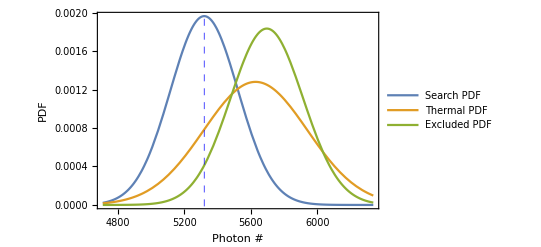

```mathematica
Plot[{PDF[NormalDistribution[searchmean,searchmeanrms],x],PDF[NormalDistribution[thermalmean,thermalrms],x],PDF[NormalDistribution[searchmean+bkg95CLnumber,(searchmean+bkg95CLnumber)/Sqrt[independentmeasurements]],x]},{x,searchmean-3searchmeanrms,searchmean+5searchmeanrms},GridLines->{{searchmean}},GridLinesStyle->Directive[Blue,Thick,Dashed],Frame->True,PlotLegends->{"Search PDF","Thermal PDF","Excluded PDF"},FrameLabel->{"Photon #","PDF"}]
```

```mathematica
Log10[(searchmean+bkg95CLnumber)/Q0Watt2PhotonNumber]*10+30
Log10[(searchmean)/Q0Watt2PhotonNumber]*10+30
%%-%
```

-186.737

-187.034

0.296515

```mathematica
sidebanddata=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First];
bkgnumber=Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms=StandardDeviation[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber/bkgrms
Sqrt[independentmeasurements]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec)*Sqrt[1328/(2430/(Qload/peakangularfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakangularfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakangularfrequency))]//N,1328]]//N
```

189.855

6.58489

28.8319

26.1924

18.8258

36.4417

15.5767

36.4417

26.1924

36.4417

28.9058

36.4417

```mathematica
sidebanddata14=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[1;;-11]],First];
bkgnumber14=Mean[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms14=StandardDeviation[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber14/bkgrms14
```

189.667

12.6524

14.9907

```mathematica
independentmeasurements11182022=Min[2430sec/(13*10^9/(peakfrequency) sec),1328]
```

242.634

### 2022 Paper input parameters (Updated May.04.2023) (2025 for microphonics paper)

-Graphics-

```mathematica
peakcoordinate=SortBy[run1data,Last][[-1]];
Qload=8.9*10^9;
Qemitterload=1.6*10^9;
amplificationfactor=1/10^(35.2/10);
NumberForm[peakcoordinate[[1]],200]
peakfrequency=peakcoordinate[[1]];
peakangularfrequency=2Pi peakfrequency;
(*Note added 0321 2025: Here the indepenent coherent measurement is roughtly 2430/(Q/f)~354, which is smaller than the 1328 averages. THis means we make a few repeated measurements within a coherence time. This should improve the statistic on thermal noise by \sqrt{1328/354}*)
independentmeasurements=Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]
photonnumberperJoulePeakfrequency=1.602176565*10^-19 Joule/eV*peakfrequency/sec*4.135667696×10^−15 eV sec/Joule(*Here I used h not hbar, so it is appropriate to use f, instead of \omega*)
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
signalregionbackground=%/photonnumberperJoulePeakfrequency/Joule
signalregionbackground/Sqrt[independentmeasurements]
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-4;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule//Total
%/photonnumberperJoulePeakfrequency/Joule
%/Sqrt[independentmeasurements]
```

1.29804120494749×10^9

686.043

8.60091×10^-25

3.13272×10^-21 Joule

3642.31

139.06

1.55823×10^-21 Joule

1811.7

69.1688

```mathematica
signalregionbackground
```

3642.31

```mathematica
independentmeasurements=Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]
```

686.043

```mathematica
2430sec/(Qload/(peakfrequency) sec)
```

354.409

Emitter cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
0.6*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

0.486765

26.8732

Emitter Q factor

```mathematica
Qemitterload=1/(1/(4.5*10^10)+1/(1.8*10^9)+1/(2.9*10^11))
```

1.7205×10^9

```mathematica
(*Note added 11/08/2022; I believe this is the integrated power in the cavity using the measured E fields and H fields*)
power=1706.8665784314976;
Eacc=-709.5009351205365;
lowPphotoncount=1/2ϵ0 power*V^2/m^2*m^3*(6.2*10^6 /Eacc)^2/photonnumberperJoulePeakfrequency/Joule
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
lowPphotoncount photonnumberperJoulePeakfrequency
% peakangularfrequency/(4.5*10^10)
Log10[%*10^3]*10(*to dBm*)
```

6.70876×10^23

0.577014

2.73527

34.37

0.577014

0.104578

20.1944

Receiver cavity power. Alex R provided stored energy being 0.6J. We can derive the power in dBm as in equilibrium, p=-\omega/Q E

```mathematica
4.8*10^-21*peakfrequency/Qemitterload
Log10[%*10^3]*10(*to dBm*)
```

3.62139×10^-21

-174.411

```mathematica
peakangularfrequency
peakfrequency
```

8.15583×10^9

1.29804×10^9

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*Hz/Watt*Joule//Total
%*peakangularfrequency/Qload/Joule
Log10[%*10^3]*10(*to dBm*)
```

4.98587×10^-22 Joule

4.56898×10^-22

-183.402

```mathematica
Log10[Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*10^3]*10//N
```

4.34294 Log[2056.95 Mean[sidebanddata]]

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[-1;;-1]],First]*Qextreceiver/Q0receiver*10^3]*10//N
Log10[Mean[0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First]]*Qextreceiver/Q0receiver*10^3]*10//N
```

-187.034

-151.834

0.162722

-0.169057

{-190.641}

-194.634

```mathematica
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First];
Q0receiver=3*10^10;
Qextreceiver=1.3*10^10;
Log10[Total[%%%]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N(*What we are measuring are P_ext = E_0 ω/Q_ext; What we want to report is P_cav = E_0/Q_0; so P_cav=P_ext Q_ext/Q_0 *)
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10//N
independentmeasurements14=Min[1.83*345sec/(Qload/(peakfrequency) sec)*Sqrt[1.83*345/(345/(Qload/peakfrequency))]//N,345]
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1+1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%
Log10[Total[0.001*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]](1-1/Sqrt[independentmeasurements14])*Qextreceiver/Q0receiver*(0.3Hz/Hz)*10^3]*10-%%%
```

-186.789

-151.589

326.171

0.234049

-0.247384

```mathematica
Q0Watt2PhotonNumber=(Q0receiver/peakangularfrequency)*2Pi*Joule/photonnumberperJoulePeakfrequency/Joule(*Here I am integrating over the window in frequency, not in angular frequency, so 2Pi is needed*)
```

2.68713×10^25

```mathematica
Qextreceiver/Q0receiver
```

0.433333

```mathematica
Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]Watt*(Qload)/(peakangularfrequency Hz)*Qextreceiver/Q0receiver(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[run1data,Last][[-10;;-1]]Watt*(Qload)/(peakangularfrequency Hz)*(0.3Hz/Hz)*2Pi Hz/Watt*Joule/photonnumberperJoulePeakfrequency/Joule//Total
```

1578.33

3642.31

```mathematica
Qload
Qextreceiver
```

8.9×10^9

1.3×10^10

```mathematica
searchmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
searchmeanrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements] Q0Watt2PhotonNumber
thermalmean=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz) Q0Watt2PhotonNumber
thermalrms=Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data14,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)/Sqrt[independentmeasurements14] Q0Watt2PhotonNumber
```

5320.22

203.121

5628.62

311.659

```mathematica
10^(1.8/10)*3.5
```

5.29746

```mathematica
Log10[Total[0.001*amplificationfactor*10^(#[[2]]/10)&/@SortBy[SortBy[run1data,Last][[-10;;-1]],First]]*Qextreceiver/Q0receiver*(0.3Hz/Hz)]*10+30
```

-187.034

```mathematica
bkg95CLnumber=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurements]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

375.925

```mathematica
Plot[{PDF[NormalDistribution[searchmean,searchmeanrms],x],PDF[NormalDistribution[thermalmean,thermalrms],x],PDF[NormalDistribution[searchmean+bkg95CLnumber,(searchmean+bkg95CLnumber)/Sqrt[independentmeasurements]],x]},{x,searchmean-3searchmeanrms,searchmean+5searchmeanrms},GridLines->{{searchmean}},GridLinesStyle->Directive[Blue,Thick,Dashed],Frame->True,PlotLegends->{"Search PDF","Thermal PDF","Excluded PDF"},FrameLabel->{"Photon #","PDF"}]
```

-Graphics-

```mathematica
Log10[(searchmean+bkg95CLnumber)/Q0Watt2PhotonNumber]*10+30
Log10[(searchmean)/Q0Watt2PhotonNumber]*10+30
%%-%
```

-186.737

-187.034

0.296515

```mathematica
sidebanddata=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data,Last][[1;;-11]],First];
bkgnumber=Mean[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms=StandardDeviation[sidebanddata]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber/bkgrms
Sqrt[independentmeasurements]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(13*10^9/(peakangularfrequency) sec),1328]]//N
Sqrt[Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(Qload/(peakangularfrequency) sec)*Sqrt[1328/(2430/(Qload/peakangularfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakfrequency))]//N,1328]]//N
Sqrt[Min[2430sec/(6*10^9/(peakangularfrequency) sec)*Sqrt[1328/(2430/(6*10^9/peakangularfrequency))]//N,1328]]//N
```

189.855

6.58489

28.8319

26.1924

18.8258

36.4417

15.5767

36.4417

26.1924

36.4417

28.9058

36.4417

```mathematica
sidebanddata14=0.001*10^(#[[2]]/10)*amplificationfactor&/@SortBy[SortBy[run1data14,Last][[1;;-11]],First];
bkgnumber14=Mean[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule(*The spectrum is measured in freuquency, averaging over 1 Hz, so multiply by 2Pi 1Hz*)
bkgrms14=StandardDeviation[sidebanddata14]Watt*(Qload)/(peakangularfrequency Hz)(0.3Hz/Hz)*(2Pi Hz)/Watt*Joule/photonnumberperJoulePeakfrequency/Joule
bkgnumber14/bkgrms14
```

189.667

12.6524

14.9907

```mathematica
independentmeasurements
```

686.043

```mathematica
Min[2430sec/(Qload/(peakfrequency) sec)*Sqrt[1328/(2430/(Qload/peakfrequency))]//N,1328]
```

686.043

```mathematica
independentmeasurementsold=Min[2430sec/(Qload/(peakfrequency) sec),1328]
```

354.409

```mathematica
independentmeasurementsold*Sqrt[1328/(2430/(Qload/peakfrequency))]
```

686.043

Considering only the measurement time before drifting away more than one \omega/Q

```mathematica
independentmeasurements03212025=Min[peakfrequency/Qload/(5.7 Hz/Hz/(6041sec))/(Qload/(peakfrequency) sec),1328]
```

22.544

```mathematica
peakfrequency Hz/Qload/(5.7 Hz/(6041sec))
```

154.573 sec

```mathematica
bkg95CLnumber=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurementsold]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

537.901

```mathematica
bkg95CLnumber2025=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurements03212025]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

3045.78

Now including the effect of repeated measurement (more than one measurement per coherence time, on the noise level)

```mathematica
bkg95CLnumber=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurementsold*Sqrt[1328/(2430/(Qload/peakfrequency))]]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

375.925

```mathematica
bkg95CLnumber2025=x/.FindRoot[CDF[NormalDistribution[searchmean+x,(searchmean+x)/Sqrt[independentmeasurements03212025*Sqrt[1328/(2430/(Qload/peakfrequency))]]],searchmean]/(1-CDF[NormalDistribution[thermalmean,thermalrms],searchmean])-0.05,{x,searchmeanrms}][[1]]
```

CompiledFunction::cfsa: Argument 5320.22+x at position 2 should be a machine-size real number.

1885.55

### Plotting

```mathematica
lowPphotonEXPcount=6.698648173348856*^23;(*6.965493438344756*^23;*)
```

```mathematica
{resultsG,resultsGwR,resultsGwZR,resultsGwithDerivatives,resultsGwRwithDerivatives,resultsGwRZwithDerivatives,resultsGwRZfullwithDerivatives}=Import[NotebookDirectory[]<>"..\\..\\DarkSRF\\CavitingBSM\\research\\Gcalculationresults.m"];
```

{{1000,7.0223×10^-14},{5000,1.75557×10^-12},{10000,7.0223×10^-12},{50000,1.75557×10^-10},{100000,7.0223×10^-10},{500000,1.75557×10^-8},{1000000,7.0223×10^-8},{5000000,1.75559×10^-6},{10000000,7.02253×10^-6},{50000000,0.000175788},{1.×10^8,0.000705908},{2.×10^8,0.00286828},{3.×10^8,0.00662349},{4.×10^8,0.0122082},{5.×10^8,0.0234615},{6.×10^8,0.0365097},{7.×10^8,0.0528782},{8.×10^8,0.0723744},{9.×10^8,0.0976879},{1.×10^9,0.127551},{1.1×10^9,0.165348},{1.2×10^9,0.212919},{1.3×10^9,0.27127},{1.4×10^9,0.00047894},{1.5×10^9,0.0000371615},{1.6×10^9,2.87586×10^-6},{1.7×10^9,4.9028×10^-7},{1.8×10^9,9.593×10^-8},{1.9×10^9,2.06774×10^-8},{2.×10^9,4.75795×10^-9},{2.1×10^9,1.14475×10^-9},{2.2×10^9,2.83613×10^-10},{2.3×10^9,7.14362×10^-11},{2.4×10^9,1.80666×10^-11},{2.5×10^9,4.52079×10^-12},{2.6×10^9,1.09539×10^-12},{2.7×10^9,2.46889×10^-13},{2.8×10^9,4.6696×10^-14},{2.9×10^9,4.34188×10^-15},{3.×10^9,2.25153×10^-15},{5000000000,2.5547×10^-22},{8000000000,8.14287×10^-33},{10000000000,1.18026×10^-39},{20000000000,3.92669×10^-73}}

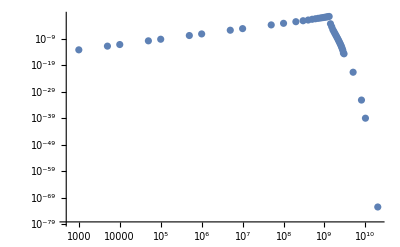

```mathematica
SortBy[resultsGwRZfullwithDerivatives,1]
ListLogLogPlot[%]
```

```mathematica
signalregionbackgroundSTD=signalregionbackground/Sqrt[independentmeasurements]
```

139.06

```mathematica
bkg95CLnumber
```

375.925

```mathematica
98.7*10^(36.8/10)/10^(38/10)/20*1.4
```

5.24101

```mathematica
(*mass in units of eV*)
masstofrequency[m_]:=(0.2*10^-6/m/(3*10^8))^-1
frequencytomass[f_]:=(0.2*10^-6*2Pi)/( 3*10^8/f)
planckconstanteVseC=4.1357*10^-15/2/Pi;
```

```mathematica
peakangularfrequency
```

8.15583×10^9

9.61512×10^-13

0.000831363

```mathematica
Sqrt[5^2+3.1^2]
```

5.88303

```mathematica
mismatch=Sqrt[5.7^2+3.1^2+3.0^2+3.1^2]
```

7.79166

```mathematica
(*Should we justify for a smaller mismatch?*)
mismatch=Sqrt[3.5^2+3.1^2]
(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+2*peakangularfrequency*2Pi mismatch)
suppression=(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+(2Pi mismatch)^2)
suppression=(peakangularfrequency/ Q0receiver)^2/((peakangularfrequency /Q0receiver)^2+(2*2Pi mismatch)^2)
```

4.67547

6.16951×10^-13

0.000342449

0.0000214099

```mathematica
mismatch=Sqrt[5.7^2+3.1^2*2+3.0^2]
(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+2*peakangularfrequency*2Pi mismatch)
suppression=(peakangularfrequency/ Q0receiver)^2/((peakangularfrequency /Q0receiver)^2+(2*2Pi mismatch)^2)
```

7.79166

3.70208×10^-13

7.70923×10^-6

```mathematica
mismatch=Sqrt[(5.7^2+3.0^2)*2.0^2/5.7^2+3.1^2*2]
(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+2*peakangularfrequency*2Pi mismatch)
suppressionprime=(peakangularfrequency/ Q0receiver)^2/((peakangularfrequency /Q0receiver)^2+(2*2Pi mismatch)^2)
```

4.93235

5.8482×10^-13

0.000019238

```mathematica
mismatch=Sqrt[(5.7^2+3.0^2)*2.0^2/5.7^2+3.1^2]
(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+2*peakangularfrequency*2Pi mismatch)
suppressionprimeprime=(peakangularfrequency/ Q0receiver)^2/((peakangularfrequency /Q0receiver)^2+(2*2Pi mismatch)^2)
```

3.83641

7.51884×10^-13

0.0000317988

```mathematica
mismatch=0
(2peakangularfrequency/ Q0receiver)^2/((2peakangularfrequency /Q0receiver)^2+2*peakangularfrequency*2Pi mismatch)
suppressionheaven=(peakangularfrequency/ Q0receiver)^2/((peakangularfrequency /Q0receiver)^2+(2*2Pi mismatch)^2)
```

0

1.

1.

0.271861

Note that it seems our PRL used bkg95 around 248 and now my calculation is around 375. There is a mismatch. I believe 248 was a very old calculation where I was still correcting the 2Pis. (03/25/2025)

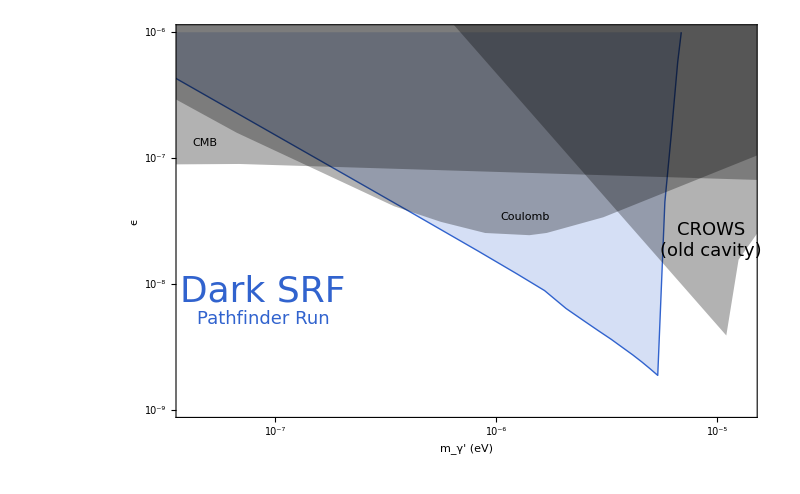

```mathematica
results11142020updated01242023ZL=ListLogLogPlot[{
(*{#[[1]]/sec plankunbar/eV,(1/Sqrt[1800/(Qrec/(2Pi*1.3*10^9))]5Sqrt[lowPbkg]/(#[[2]]^2*Qrec^2*lowPphotoncount))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],
{ #[[1]]/sec plankunbar/eV,(1/Sqrt[1800/(Qrec/(2Pi*1.3*10^9))]5highPbkg/(#[[2]]^2*Qrec^2*highPphotoncount))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],*)
(* #[[1]]/sec plankunbar/eV,(756/Sqrt[1300]*2/(#[[2]]^2*Qload^2*lowPphotonEXPcount*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1]*)
(*{ #[[1]]/sec plankunbar/eV,((signalregionbackground+bkgrmssideband*2)/(#[[2]]^2*Qload^2*lowPphotonEXPcount*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],*)
{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*suppression(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1]
(*,
{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*suppressionprime(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],
{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*suppressionprimeprime(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*suppressionheaven(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1]*)
}
,PlotRange->{{4*10^-8,1.35*10^-5},{10^-9,10^-6}},Frame->True,FrameStyle->Black,BaseStyle->24,ImageSize->800,FrameLabel->{{Style[Rotate["ϵ",-Pi/2],FontFamily->"CMU Serif",30],""},{Style["m_γ' (eV)",FontFamily->"CMU Serif",30],Style["Frequency (Hz)",FontFamily->"CMU Serif"]}},Joined->True,PlotStyle->{{Thick,ColorData[colorselecitonumber][2]},{Dashed,Blue},{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->Top,FrameTicks->{{LogTicks[10,10^-25,10^12,TickLabelStep->1],StripTickLabels[LogTicks[10,10^-25,10^12,TickLabelStep->1]]},{LogTicks[10,10^-25,10^12,TickLabelStep->1],Join[Table[{frequencytomass[10^log10f],If[Mod[log10f,1]==0,Superscript["10",log10f]],{0.025,0}},{log10f,-10,15,1}],Flatten[Table[{frequencytomass[minorstep*10^log10f],,{0.015,0}},{log10f,-10,10,1},{minorstep,2,9,1}],1]]}}];
Show[results11142020updated01242023ZL,otherlimits,
Epilog->{Inset[Style["Dark SRF",ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",36], Scaled[{0.15,0.32}]],Inset[Style["Pathfinder Run",ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",18], Scaled[{0.15,0.25}]],
Inset[ImageResize[-Graphics-,400],Scaled[{0.15,0.14}]],(*Inset[LineLegend[{Thick,Dashed,DotDashed},{"Run0 Result","Thermal subtraction"}], Scaled[{0.2,0.45}]],*)Inset[Style["CMB",Black],Scaled[{0.05,0.7}]],Inset[Style["Coulomb",FontFamily->"CMU Serif",Black],Scaled[{0.6,0.51}]],Inset[Style["CROWS\n(old cavity)",FontFamily->"CMU Serif",18,Black],Scaled[{0.92,0.45}]]}]
```

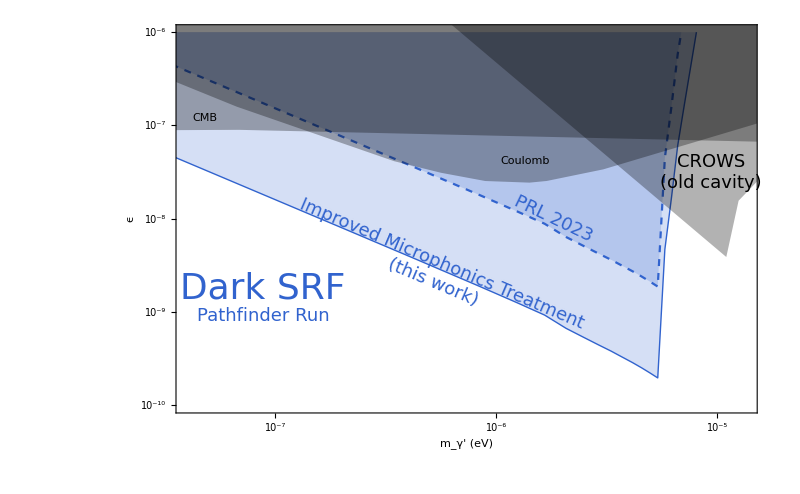

```mathematica
results11142020updated03252025ZL=ListLogLogPlot[{
{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)(*bkg95CLnumber; here, instead of ~375 of my new calculation, let me use the old ~248 number to reproduce PRL*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*suppression(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1],
{ #[[1]]/sec plankunbar/eV,((*signalregionbackgroundSTD*2*)bkg95CLnumber/(#[[2]]^2*Qload^2*lowPphotonEXPcount*(*0.86 is the mean value of power suppression in our paper*)0.86*(*This additional factor is because we avearged over 35mins, we assume apart from the first few mins, the rest signal rate is zero*)(peakfrequency Hz/Qload/(5.7 Hz/(6041sec))/(35min*60sec/min))(*(peakcoordinate[[1]]/Qload/Sqrt[peakcoordinate[[1]]^2/Qload^2+5^2+3^2])^2)*)))^(1/4)}&/@SortBy[resultsGwRZfullwithDerivatives,1]
}
,PlotRange->{{4*10^-8,1.35*10^-5},{1*10^-10,10^-6}},Frame->True,FrameStyle->Black,BaseStyle->24,ImageSize->800,FrameLabel->{{Style[Rotate["ϵ",-Pi/2],FontFamily->"CMU Serif",30],""},{Style["m_γ' (eV)",FontFamily->"CMU Serif",30],Style["Frequency (Hz)",FontFamily->"CMU Serif"]}},Joined->True,PlotStyle->{{Dashed,ColorData[colorselecitonumber][2]},{Thick,ColorData[colorselecitonumber][2]},{Dotted,Blue},{Dashed,Cyan},{Dotted,Red},{Dotted,Blue}},Filling->Top,FrameTicks->{{LogTicks[10,10^-25,10^12,TickLabelStep->1],StripTickLabels[LogTicks[10,10^-25,10^12,TickLabelStep->1]]},{LogTicks[10,10^-25,10^12,TickLabelStep->1],Join[Table[{frequencytomass[10^log10f],If[Mod[log10f,1]==0,Superscript["10",log10f]],{0.025,0}},{log10f,-10,15,1}],Flatten[Table[{frequencytomass[minorstep*10^log10f],,{0.015,0}},{log10f,-10,10,1},{minorstep,2,9,1}],1]]}}];
Show[results11142020updated03252025ZL,otherlimits,
Epilog->{Inset[Style["Dark SRF",ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",36], Scaled[{0.15,0.32}]],Inset[Style["Pathfinder Run",ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",18], Scaled[{0.15,0.25}]],
Inset[Style[Rotate["PRL 2023",-Pi/7],ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",18], Scaled[{0.65,0.5}]],
Inset[Style[Rotate["Improved Microphonics Treatment\n(this work)",-Pi/7.8],ColorData[colorselecitonumber][2],FontFamily->"CMU Serif",18], Scaled[{0.45,0.36}]],
Inset[ImageResize[-Graphics-,400],Scaled[{0.15,0.14}]],(*Inset[LineLegend[{Thick,Dashed,DotDashed},{"Run0 Result","Thermal subtraction"}], Scaled[{0.2,0.45}]],*)Inset[Style["CMB",Black],Scaled[{0.05,0.76}]],Inset[Style["Coulomb",FontFamily->"CMU Serif",Black],Scaled[{0.6,0.65}]],Inset[Style["CROWS\n(old cavity)",FontFamily->"CMU Serif",18,Black],Scaled[{0.92,0.62}]]}]
```

```mathematica
Export[NotebookDirectory[]<>"run0result_03262025_ZL.pdf",%]
```

C:\Users\Zhen\Documents\GitHub\JitterModel\Research\run0result_03262025_ZL.pdf